1<l without a cap

```mathematica
PT1[l_,p_]:=   p^l*(1/2^(l-1))*(1-p)
```

2 < l with cap

```mathematica
PT2[l_,p_]:=p^l/2^(l-1)
```

l=1

l=0

```mathematica
PT3[p_]:=1-p
h[τ_]:=1/(1+1/τ)
En[τ_]:=-Sum[PT1[l,τ]*Log[PT1[l,τ]],{l,1,Infinity}]-Sum[PT2[l,1/(1+1/τ)]*Log[PT2[l,1/(1+τ)]],{l,2,Infinity}]-PT3[τ]*Log[PT3[τ]]
```

```mathematica
Entips[p_]:=-p*(Sum[(l-1)p^(l-1)/2^(l-1)Log[p/2],{l,2,Infinity}]+Sum[p^(l-1)/2^(l-1)*(Log[p]),{l,2,Infinity}])-p*(1-p)(Sum[(l-1)p^(l-1)/2^(l-1)Log[p/2],{l,1,Infinity}]+Sum[p^(l-1)/2^(l-1)*(Log[p(1-p)]),{l,1,Infinity}])-(1-p)Log[1-p]
```

```mathematica
Entips[p]
```

-(1-p) Log[1-p]-p ((2 p Log[p/2])/(-2+p)^2-(p Log[p])/(-2+p))-(1-p) p ((2 p Log[p/2])/(-2+p)^2-(2 Log[-(-1+p) p])/(-2+p))

```mathematica
Simplify[-(1-p) Log[1-p]-p ((2 p Log[p/2])/(-2+p)^2-(p Log[p])/(-2+p))-(1-p) p ((2 p Log[p/2])/(-2+p)^2-(2 Log[-(-1+p) p])/(-2+p))]
```

((2-3 p+p^2) Log[1-p]+p (-p Log[4]+3 p Log[p]-2 (-1+p) Log[-(-1+p) p]))/(-2+p)

```mathematica
((2-3 p+p^2) Log[1-p]+p (-p Log[4]+3 p Log[p]-2 (-1+p) (Log[(1-p)] +Log[p])))/(-2+p)
```

((2-3 p+p^2) Log[1-p]+p (-p Log[4]+3 p Log[p]-2 (-1+p) (Log[1-p]+Log[p])))/(-2+p)

```mathematica
Simplify[((2-3 p+p^2) Log[1-p]+p (-p Log[4]+3 p Log[p]-2 (-1+p) (Log[1-p]+Log[p])))/(-2+p)]
```

(-(-2+p+p^2) Log[1-p]+p (-p Log[4]+(2+p) Log[p]))/(-2+p)

```mathematica
A[p_]:=(-(-2+p+p^2) Log[1-p]+p (-p Log[4]+(2+p) Log[p]))/(-2+p)
```

```mathematica
Sum[1/2^(l-1)*Log[1/2^(l-1)],{l,2,Infinity}]
```

-2 Log[2]

```mathematica
PT1[l_,p_]:=p^l*(1/2^(l-1))*(1-p)
```

```mathematica
PT2[l_,p_]:=p^l/2^(l-1)
```

```mathematica
PT3[p_]:=1-p
```

```mathematica
h[τ_]:=1/(1+1/τ)
```

```mathematica
τ/.Solve[PT3[h[τ]]==1/20&&τ>0]
```

{19}

```mathematica
T1=Evaluate@Table[τ/.Solve[PT1[i,h[τ]]==1/20&&τ>0],{i,1,4}]
```

{{9-4 √5,9+4 √5},{Root[1+3 #1-7 #1^2+#1^3&,2],Root[1+3 #1-7 #1^2+#1^3&,3]},τ,τ}

```mathematica
T2=Evaluate@Table[τ/.Solve[PT2[i,h[τ]]==1/20&&τ>0],{i,1,6}]
```

{{1/19},{1/9 (1+√10)},{Root[-1-3 #1-3 #1^2+4 #1^3&,1]},{Root[-2-8 #1-12 #1^2-8 #1^3+3 #1^4&,2]},{Root[-4-20 #1-40 #1^2-40 #1^3-20 #1^4+#1^5&,1]},τ}

```mathematica
Flatten[T2]
```

{1/19,1/9 (1+√10),Root[-1-3 #1-3 #1^2+4 #1^3&,1],Root[-2-8 #1-12 #1^2-8 #1^3+3 #1^4&,2],Root[-4-20 #1-40 #1^2-40 #1^3-20 #1^4+#1^5&,1],τ}

```mathematica
Root[-2-8 #1-12 #1^2-8 #1^3+3 #1^4&,2]
```

Root[-2-8 #1-12 #1^2-8 #1^3+3 #1^4&,2]

```mathematica
N[Root[-2-8 #1-12 #1^2-8 #1^3+3 #1^4&,2]]
```

3.8845

```mathematica
N[Root[-4-20 1-40 #1^2-40 #1^3-20 #1^4+#1^5&,1]]
```

21.9092

```mathematica
21.Root[-4-20 #1-40 #1^2-40 #1^3-20 #1^4+#1^5&,1]910819524361653
```

```mathematica
b[x_]:=0.1/; x<19
c[x_]:=0.2/;T1[[1]][[1]]<x<T1[[1]][[2]]
e[x_]:=0.3/;T1[[2]][[1]]<x<T1[[2]][[2]]
f[x_]:=0.4/;0.4624752955742644<x
g[x_]:=0.5/;1.4084984212223908<x
i[x_]:=0.6/;3.8844993877898344<x
j[x_]:=0.7/;21.90915625866726<x
```

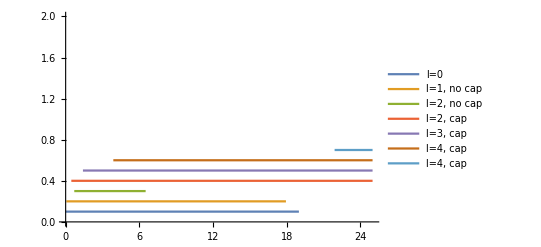

```mathematica
Plot[{b[x],c[x],e[x],f[x],g[x],i[x],j[x]},{x,0,25},PlotRange->{0,2}, PlotLegends->{"l=0","l=1, no cap","l=2, no cap", "l=2, cap","l=3, cap","l=4, cap", "l=4, cap"}]
```